### Step R and ϕ (0)

```mathematica
JU[U_]=1+U(Log[U]-1)
```

1+U (-1+Log[U])

```mathematica
D[JU[U],U]
```

Log[U]

```mathematica
Simplify[D[JU[U],U]==Log[U]]
```

True

```mathematica
Wbar[η_]=0.595+η/3.7+η^4.55
```

0.595+0.27027 η+η^4.55

```mathematica
D[Wbar[η],η]
```

0.27027+4.55 η^3.55

```mathematica
Simplify[D[Wbar[η],η]==1/3.7+4.55 η^3.55]
```

True

```mathematica
q[Wbar_]=(2 Wbar-1)/(1-Wbar)
```

(-1+2 Wbar)/(1-Wbar)

```mathematica
Simplify[D[q[Wbar],Wbar]]
```

1/(-1+Wbar)^2

```mathematica
Simplify[D[q[Wbar],Wbar]==(Wbar-1)^-2]
```

True

```mathematica
GU[U_,q_]=(U-1-(1-1/U^(1+q))/(1+q))/((2+q)Ju[U])
```

(-1+U-(1-U^(-1-q))/(1+q))/((2+q) Ju[U])

```mathematica
Simplify[Expand[GU[U,q]]]
```

-(2+q-U-q U-U^(-1-q))/((2+3 q+q^2) Ju[U])

```mathematica
Simplify[GU[U,q]==(U(1+q)-(2+q)+U^(-1-q))/((1+q)(2+q) Ju[U])]
```

True

```mathematica
D[GU[U,q],U]
```

(1+((-1-q) U^(-2-q))/(1+q))/((2+q) Ju[U])-((-1+U-(1-U^(-1-q))/(1+q)) Ju'[U])/((2+q) Ju[U]^2)

```mathematica
((-1+U-(1-U^(-1-q))/(1+q)) Ju'[U])/((2+q) Ju[U]^2)/GU[U,q]
```

Ju'[U]/Ju[U]

```mathematica
Simplify[D[GU[U,q],U]==(1-U^(-2-q))/((2+q) Ju[U])-(Ju'[U]/Ju[U])GU[U,q]]
```

True

```mathematica
D[GU[U,q],q]
```

-(-1+U-(1-U^(-1-q))/(1+q))/((2+q)^2 Ju[U])+((1-U^(-1-q))/(1+q)^2-(U^(-1-q) Log[U])/(1+q))/((2+q) Ju[U])

```mathematica
(-1+U-(1-U^(-1-q))/(1+q))/((2+q)^2 Ju[U])/GU[U,q]
```

1/(2+q)

```mathematica
Simplify[(1-U^(-1-q))/(1+q)^2-(U^(-1-q) Log[U])/(1+q)]
```

(U^(-1-q) (-1+U^(1+q)-(1+q) Log[U]))/(1+q)^2

```mathematica
Simplify[D[GU[U,q],q]==(((U^(1+q)-1)-(1+q) Log[U])/(Ju[U] U^(1+q)(1+q)^2)-GU[U,q])/(2+q)]
```

True

```mathematica
CForm[(((1-U^(-1-q))/(1+q)^2-(U^(-1-q) Log[U])/(1+q))/Ju[U]-GU[U,q])/(2+q)]
```

(-((-1 + U - (1 - Power(U,-1 - q))/(1 + q))/((2 + q)*Ju(U))) + 
     ((1 - Power(U,-1 - q))/Power(1 + q,2) - (Power(U,-1 - q)*Log(U))/(1 + q))/Ju(U))/(2 + q)

```mathematica
etaBar[Zbarb_]=1.75 10^-3 Zbarb+0.37(1-Exp[-0.015 Zbarb^1.3])
```

0.37 (1-ⅇ^(-0.015 Zbarb^1.3))+0.00175 Zbarb

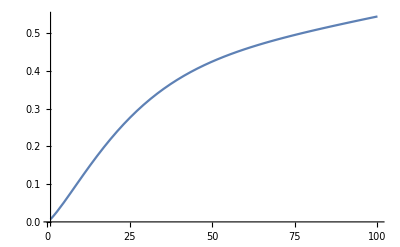

```mathematica
Plot[etaBar[z],{z,1,100}]
```

```mathematica
D[etaBar[Zbarb],Zbarb]
```

0.00175+0.007215 ⅇ^(-0.015 Zbarb^1.3) Zbarb^0.3

```mathematica
Simplify[D[etaBar[Zbarb],Zbarb]==0.00175+0.007215 Exp[-0.015 Zbarb^1.3] Zbarb^0.3]
```

True

```mathematica
R[Zbarb_,E0_]=1-etaBarZ[Zbarb] WbarZ[Zbarb] (1-G[E0,Zbarb])
```

1-etaBarZ[Zbarb] (1-G[E0,Zbarb]) WbarZ[Zbarb]

```mathematica
D[R[Zbarb, E0],Zbarb]
```

-(1-G[E0,Zbarb]) WbarZ[Zbarb] etaBarZ'[Zbarb]-etaBarZ[Zbarb] (1-G[E0,Zbarb]) WbarZ'[Zbarb]+etaBarZ[Zbarb] WbarZ[Zbarb] G^(0,1)[E0,Zbarb]

```mathematica
Simplify[D[R[Zbarb, E0],Zbarb]==etaBarZ[Zbarb] (WbarZ[Zbarb] Derivative[0,1][G][E0,Zbarb]-(1-G[E0,Zbarb]) WbarZ'[Zbarb])-(1-G[E0,Zbarb]) WbarZ[Zbarb] etaBarZ'[Zbarb]]
```

True

```mathematica
D[R[Zbarb, E0],E0]
```

etaBarZ[Zbarb] WbarZ[Zbarb] G^(1,0)[E0,Zbarb]

```mathematica
Simplify[D[R[Zbarb, E0],E0]==etaBarZ[Zbarb] WbarZ[Zbarb] Derivative[1,0][G][E0,Zbarb]]
```

True

```mathematica
Phi0[etaBar_,U0_]=1+33/10(1-1/U0^(2-23/10 etaBar))etaBar^(6/5)
```

1+33/10 etaBar^(6/5) (1-U0^(-2+(23 etaBar)/10))

```mathematica
Simplify[D[Phi0[etaBar,U0],etaBar]]
```

-(33 etaBar^(1/5) (12 (-U0^2+U0^(23 etaBar/10))+23 etaBar U0^(23 etaBar/10) Log[U0]))/(100 U0^2)

```mathematica
Simplify[D[Phi0[etaBar,U0],etaBar]==etaBar^(1/5)(396/100 (1-U0^(23/10etaBar-2))-759/100 etaBar U0^(23/10etaBar-2) Log[U0])]
```

True

```mathematica
D[Phi0[etaBar,U0],U0]
```

-33/10 etaBar^(6/5) (-2+(23 etaBar)/10) U0^(-3+(23 etaBar)/10)

```mathematica
Simplify[D[Phi0[etaBar,U0],U0]==-33/10 etaBar^(6/5) (-2+23/10 etaBar) U0^(23/10 etaBar-3)]
```

True

```mathematica
3*0.869565
```

2.6087